# The Infamous Grapefruit Problem

```mathematica
Neil McBlane - 2050386
```

#### 1.1 - Optimal firing angle in the absence of drag

```mathematica
Clear[v,θ,g,u,ux,uy];
x[v_,θ_,t_]:=ReplaceAll[τ->t][v Cos[θ]τ]
y[v_,θ_,t_]:=ReplaceAll[τ->t][v Sin[θ]τ-(g τ^2)/2]
{t0,tf}=Values[Solve[y[v,θ,t]==0,t]];
range = x[v,θ,tf];
FullSimplify[Solve[{D[range,θ]==0,0≤θ≤π/2},θ]]
```

{{θ→π/4}}

This is the expected optimal angle of 45°

```mathematica
g=9.81;
θ=π/4;
u=Solve[{range==1000,v≥0},v][[1]];
ut=v/.u
ux=v Cos[θ]/.u
uy=v Sin[θ]/.u
```

99.0454

70.0357

70.0357

#### 1.2 - Graphical proof of the optimal angle

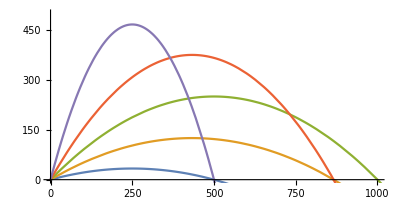

```mathematica
ParametricPlot[Evaluate[Table[{x[ut,θ,t],y[ut,θ,t]},{θ,π/12,(5π)/12,π/12}]],{t,0,100},PlotRange->{{0,1000},{0,500}}]
```

The green line corresponds to θ = 45°, clearly demonstrating it is the optimal angle.

#### 1.3 - Including drag

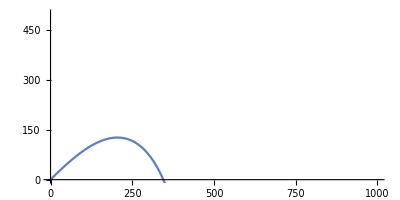

```mathematica
ρ = 1.225;
m = 0.5;
r = 0.05^2;
g=9.81;

Clear[θ,v]
sol=ParametricNDSolve[{x''[t]+(ρ r √(x'[t]^2+y'[t]^2))/(2 m) x'[t]==0,
y''[t]+g+(ρ r √(x'[t]^2+y'[t]^2))/(2 m) y'[t]==0,x'[0]==v Cos[θ],y'[0]==v Sin[θ],x[0]==0,y[0]==0},{x,y},{t,0,30},{v,θ}];
θ = π/4;
v=99.0454;

ParametricPlot[{Evaluate[x[v,θ][t]/.sol],Evaluate[y[v,θ][t]/.sol]},{t,0,20}, PlotRange->{{0,1000},{0,500}}]
```

The range is severly impacted - reaching roughly 350m only.

#### 1.4 - Finding the optimal angle with drag

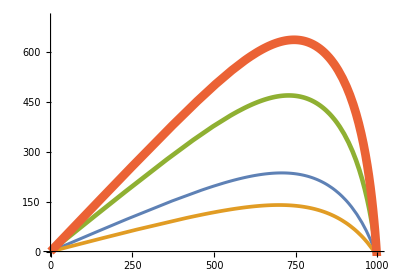

```mathematica
relThick[v_]:=(v/8800)^2
ParametricPlot[{{Evaluate[x[650,0.4][t]/.sol],Evaluate[y[650,0.4][t]/.sol]},{Evaluate[x[720,0.25][t]/.sol],Evaluate[y[720,0.25][t]/.sol]},
{Evaluate[x[800,0.67][t]/.sol],Evaluate[y[800,0.67][t]/.sol]},
{Evaluate[x[1100,0.8][t]/.sol],Evaluate[y[1100,0.8][t]/.sol]}},{t,0,30},PlotRange->{{0,1000},{0,700}},
PlotStyle->{Thickness[relThick[650]],Thickness[relThick[720]],Thickness[relThick[800]],Thickness[relThick[1100]]}]
```

With line thickness set to a function of the velocity, we see the optimal firing angle is roughly 0.4 radians. This line is shown in blue, and is the thinnest.

#### 1.5 - To trial and error, and beyond

```mathematica
clear[v];

impactTime[v_,θ_]:=FindRoot[y[v,θ][t]/.sol,{t,20}][[1]]
rangeFunc[v_,θ_]:=x[v,θ][t/.impactTime[v,θ]]/.sol

velocityFunc[r_,θ_]:=Module[{v=0,range=0},
							While[rangeFunc[v,θ]<r,v+=10];
							While[rangeFunc[v,θ]>r,v-=1];
							While[rangeFunc[v,θ]<r,v+=0.1];
							v
							]

angleFunc[r_]:=Module[{θ=0.1,oldVel=1,newVel=0},
					While[newVel<oldVel,
						{newVel=velocityFunc[r,(θ+0.01)],
						oldVel=velocityFunc[r,θ],
						θ += 0.01}];

					While[newVel<oldVel,
						{newVel=velocityFunc[r,(θ-0.001)],
						oldVel=velocityFunc[r,θ],
						θ -= 0.001}];

					θ
					]
angleFunc[1000]
```